{{8,7371},{1,7435},{9,37101},{4,7370},{5,7496},{7,7343},{2,7368},{3,7373},{6,7440},{10,3703}}

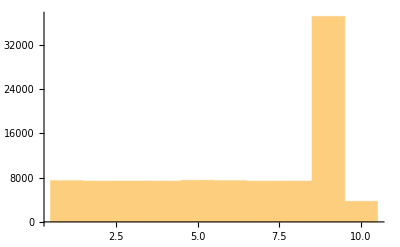

```mathematica
pop =BinPopGenerator[10,10];
fpheno :=Function[{x}, {1,1,1,1,1,1,1,1,5,0.5}];
popFitness = fpheno[pop]; (*Calculates fitness(pheno(pop))*)
t =Table[SelectParentByWheel[pop, popFitness], {i,1,100000}];
Tally[t]
Histogram[t, 10]
```